```mathematica
(*setup information*)
n = 4; (*number of elements*)
h = 1/200; (*time step size*)
totalTime = 50; (*total time of simulation*)
numSteps = totalTime/h; (*total discrete steps*)
startPos =0;
endPos= 1;
restPos = Table[startPos + i * (endPos-startPos) / n, {i, 0, n}];
restVals = Table[startPos + i * (endPos-startPos) / n, {i, 1, n}];
youngs = 10^4;
poisson = 1/4;
lameα = youngs / (2 * (1 + poisson));
lameβ = youngs * poisson / (1 + poisson);
pow = 10; 
mag = youngs / 2;
selectedId = n+1; 
fixedId = 1;
initPos = 1.2 * restPos;
initPos[[fixedId]] = restPos[[fixedId]];
initVals = 1.2 * restVals;
```

```mathematica
(*variables*)
```

```mathematica
curPos = Table[Subscript[x, i], {i, 1, n+1}];
curPos[[fixedId]] = restPos[[fixedId]];
curPos
```

{0,x_2,x_3,x_4,x_5}

```mathematica
(*projection matrix*)
projM = Table[0, {i, 1, n}, {j, 1, n+1}];
row = 1;
For[i=1,i≤ n+1,
If[i ≠fixedId,projM[[row]][[i]] = 1;row+= 1];i++];
projM // MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
(*get the reduced system*)
```

```mathematica
curVars = projM.curPos
```

{x_2,x_3,x_4,x_5}

```mathematica
(*Energy*)
energy = 0;
For[i=1,i≤ n, 
dr = curPos[[i+1]] - curPos[[i]];
drRest = restPos[[i+1]] - restPos[[i]];
strain = (dr - drRest) / drRest;
energy = energy+(lameα + lameβ / 2) * strain * strain * Abs[drRest];
i++];
```

```mathematica
energy
```

20000 (-1/4+x_2)^2+20000 (-1/4-x_2+x_3)^2+20000 (-1/4-x_3+x_4)^2+20000 (-1/4-x_4+x_5)^2

```mathematica
(*gradient and hessian*)
gradient = D[energy, {curVars}]
```

{40000 (-1/4+x_2)-40000 (-1/4-x_2+x_3),40000 (-1/4-x_2+x_3)-40000 (-1/4-x_3+x_4),40000 (-1/4-x_3+x_4)-40000 (-1/4-x_4+x_5),40000 (-1/4-x_4+x_5)}

```mathematica
hessian = D[energy, {curVars, 2}]
```

{{80000,-40000,0,0},{-40000,80000,-40000,0},{0,-40000,80000,-40000},{0,0,-40000,40000}}

```mathematica
hessian // MatrixForm
```

(80000 | -40000 | 0 | 0
-40000 | 80000 | -40000 | 0
0 | -40000 | 80000 | -40000
0 | 0 | -40000 | 40000)

```mathematica
(*eigen value and eigen vectors*)
evals = Eigenvalues[hessian] // FullSimplify 
evecs = Eigenvectors[hessian] ;
For[i=1,i≤ n, evecs[[i]] = evecs[[i]] / Norm[evecs[[i]]];i++];
```

{Root1.41 × 10^5Root[-64000000000000+14400000000 #1-240000 #1^2+#1^3&,3]141283.55544951823,Root9.39 × 10^4Root[-64000000000000+14400000000 #1-240000 #1^2+#1^3&,2]93891.85421335443,40000,Root4.82 × 10^3Root[-64000000000000+14400000000 #1-240000 #1^2+#1^3&,1]4824.590337127329}

```mathematica
evals // N
```

{141284.,93891.9,40000.,4824.59}

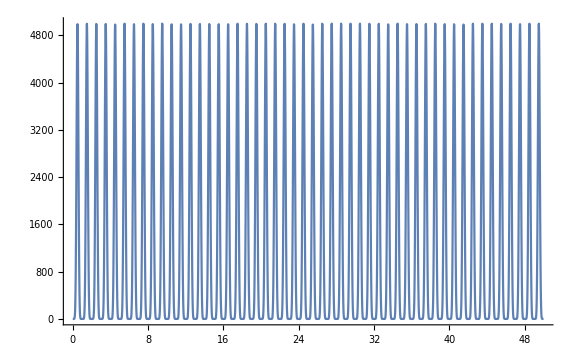

```mathematica
(*external force*)
impulse[t_] = mag*Sin[Pi t ]^pow;
Plot[impulse[t], {t, 0 ,totalTime}, PlotRange->All, ImageSize->Large]
```

```mathematica
entireImpulse[t_] = Table[impulse[t], {i, 1, n + 1}]
```

{5000 Sin[π t]^10,5000 Sin[π t]^10,5000 Sin[π t]^10,5000 Sin[π t]^10,5000 Sin[π t]^10}

```mathematica
maskMatrix = Table[0, {i, 1, n + 1}, {j, 1, n + 1}]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
maskMatrix[[selectedId]][[selectedId]] = 1
maskMatrix // MatrixForm
```

1

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
fullCoordExtForce[t_] = maskMatrix.entireImpulse[t]
```

{0,0,0,0,5000 Sin[π t]^10}

```mathematica
extForce[t_] = projM.fullCoordExtForce[t]
```

{0,0,0,5000 Sin[π t]^10}

```mathematica
(*get the eigen mode decomposition *)
constPart = (gradient - hessian.curVars) /. Thread[curVars->restVals]
E0 = energy/.Thread[curVars-> Table[0, {i, 1, n}]]
alternativeEnergy = 1/2 * curVars.(hessian.curVars) + constPart.curVars + E0
```

{0,0,0,-10000}

5000

5000-10000 x_5+1/2 (x_2 (80000 x_2-40000 x_3)+x_3 (-40000 x_2+80000 x_3-40000 x_4)+x_4 (-40000 x_3+80000 x_4-40000 x_5)+x_5 (-40000 x_4+40000 x_5))

```mathematica
(energy - alternativeEnergy) // FullSimplify
```

0

```mathematica
vecC[t_] = constPart + extForce[t];
listC = {};
For[i =1, i≤ n,
varC[s_] = evecs[[i]].vecC[s];
AppendTo[listC, varC[s]];
i++];
```

```mathematica
evals// N
```

{141284.,93891.9,40000.,4824.59}

```mathematica
(*compute theoretical solutions*)
theoαList = {};
For[i =1, i≤ n,
λ= evals[[i]];
a0 = initVals.(evecs[[i]]);
theoSol = NDSolve[{(f''[t]+λ f[t]+listC[[i]]/.{s-> t})==0,f[0]==a0,f'[0]==0},f[t],{t, 0, totalTime}, MaxStepFraction-> 1/10000];
theoα[t_] = (f[t]/.theoSol[[1]]) // FullSimplify;
AppendTo[theoαList, theoα[t]];
i++]
```

```mathematica
reducedPos[s_] = Sum[evecs[[i]]*(theoαList[[i]]/. {t-> s}), {i, 1, n}];
```

```mathematica
theoPos[s_] := Transpose[projM].reducedPos[s];
```

```mathematica
(*Discrete time list*)
timeList = {0};
For[i=1,i≤numSteps,
AppendTo[timeList, i * h];
i++] ;
```

```mathematica
(*IE solution*)
IEαList = {};
For[j=1,j≤ n,
λ= evals[[j]];
a0 = initVals.(evecs[[j]]);
IEM = {{1, -h},{λ h, 1}};
Clear[IEw1, IEw];
IEw1[m_]= {0,-h listC[[j]]/.{s-> m h}};
IEA = Inverse[IEM];
 IEw[m_]= IEA.IEw1[m];
IEα = {a0};
IEβ = {0};
IEtimeα = {{0, a0}};
For[i=1,i≤numSteps,
a =(IEA[[1,1]] IEα[[i]] + IEA[[1,2]] IEβ[[i]] + IEw[i][[1]])// N;
 b=(IEA[[2,1]] IEα[[i]] + IEA[[2,2]] IEβ[[i]] + IEw[i][[2]])// N;
AppendTo[IEα, a];
AppendTo[IEβ, b];
AppendTo[IEtimeα, {i * h, a}];
i++] ;
AppendTo[IEαList, IEα];
j++];
```

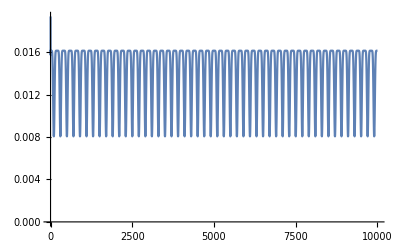

```mathematica
ListLinePlot[IEαList[[1]], PlotRange->All]
```

```mathematica
IEPos = {};
For[i = 1, i ≤   numSteps + 1,  
posInfo = Sum[IEαList[[j]][[i]]*evecs[[j]],{j, 1, n}];
posInfo = Transpose[projM].posInfo;
AppendTo[IEPos, posInfo];
i++];
```

```mathematica
(*Newmark-β*)
NMαList = {};
For[j=1,j≤ n,
λ= evals[[j]];
a0 = initVals.(evecs[[j]]);
NMM = {{1 + h^2 λ β, 0},{λ h / 2, 1}};
Clear[NMw1,NMw]; 
NMw1[m_] = {(-h^2listC[[j]]/.{s-> m h}) / 2, - h listC[[j]]/.{s-> m h}};
NMM1 ={{1 - h ^2 λ(1/2 - β), h}, {-λ h / 2, 1}};
NMA = Inverse[NMM].NMM1;
NMw[m_] = Inverse[NMM].NMw1[m];
NMα = {a0};
NMβ = {0};
NMtimeα = {{0, a0}};
For[i=1,i≤numSteps,
a =(NMA[[1,1]] NMα[[i]] + NMA[[1,2]] NMβ[[i]] + NMw[i][[1]])/.{β-> 1/4}// N;
 b=(NMA[[2,1]] NMα[[i]] + NMA[[2,2]] NMβ[[i]] + NMw[i][[2]])/.{β-> 1/4}// N;
AppendTo[NMα, a];
AppendTo[NMβ, b];
AppendTo[NMtimeα, {i * h, a}];
i++];
AppendTo[NMαList, NMα];
j++];
```

```mathematica
NMPos = {};
For[i = 1, i ≤   numSteps + 1,  
posInfo = Sum[NMαList[[j]][[i]]*evecs[[j]],{j, 1, n}];
posInfo = (Transpose[projM].posInfo) /.{β-> 1/4};
AppendTo[NMPos, posInfo];
i++];
```

```mathematica
(*BDF2*)
BDF2αList = {};
For[j=1,j≤ n,
λ= evals[[j]];
a0 = initVals.(evecs[[j]]);
BDF2M = {{1, -2h/3}, {2h λ/3, 1}};
BDF2M1 = {{4/3, 0}, {0, 4/3}};
BDF2M2 = {{-1/3, 0}, {0, -1/3}};
Clear[BDF2w1, BDF2w];
BDF2w1[m_] = {0, -2h(listC[[j]]/.{s-> m h}) /3};
(*BDF2w1[m_] = {0, -2 h varC[m h] /3};*)
BDF2A1 = Inverse[BDF2M].BDF2M1;
BDF2A2 = Inverse[BDF2M].BDF2M2;
BDF2w[m_] = Inverse[BDF2M].BDF2w1[m];

(*use IE to get the first step information*)
IEM = {{1, -h},{λ h, 1}};
IEw1= {0,-h (listC[[j]]/.{s-> h})};
(*IEw1= {0,-h varC[h]};*)
IEA = Inverse[IEM];
 IEw= IEA.IEw1;
IEα = {a0};
IEβ = {0};
a =(IEA[[1,1]] *a0 + IEA[[1,2]] * 0 + IEw[[1]])// N;
 b=(IEA[[2,1]] * a0 + IEA[[2,2]]* 0 + IEw[[2]])// N;

BDF2α = {a0, a};
BDF2β = {0, b};
BDF2timeα = {{0, a0}, {h, a}};
For[i=2,i≤numSteps,
a =(BDF2A1[[1,1]] BDF2α[[i]] + BDF2A1[[1,2]] BDF2β[[i]] + BDF2A2[[1,1]] BDF2α[[i-1]] + BDF2A2[[1,2]] BDF2β[[i - 1]] + BDF2w[i][[1]])// N;
 b=(BDF2A1[[2,1]] BDF2α[[i]] + BDF2A1[[2,2]] BDF2β[[i]] + BDF2A2[[2,1]] BDF2α[[i-1]] + BDF2A2[[2,2]] BDF2β[[i - 1]] + BDF2w[i][[2]])// N;
AppendTo[BDF2α, a];
AppendTo[BDF2β, b];
AppendTo[BDF2timeα, {i * h, a}];
i++];
AppendTo[BDF2αList, BDF2α];
j++];
```

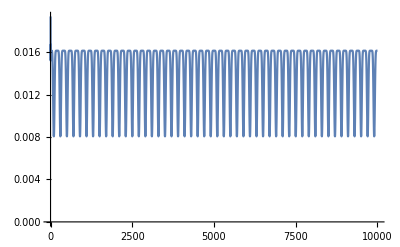

```mathematica
ListLinePlot[BDF2αList[[1]], PlotRange->All]
```

```mathematica
BDF2Pos = {};
For[i = 1, i ≤   numSteps + 1, 
posInfo = Sum[BDF2αList[[j]][[i]]*evecs[[j]],{j, 1, n}];
posInfo = (Transpose[projM].posInfo);
AppendTo[BDF2Pos, posInfo];
i++];
```

```mathematica
(*TRBDF2 solution*)
TRBDF2αList= {};
For[j=1,j≤ n,
λ= evals[[j]];
a0 = initVals.(evecs[[j]]);
TRBDF2M = {{1, -γ h}, {γ λ h, 1}};
TRBDF2M1 = {{1, γ h}, {-γ λ h, 1}};
Clear[TRBDF2w,TRBDF2w1,  TRBDF2w2, TRBDF2w3];
TRBDF2w[m_] = {0, -2  γ * h *  (listC[[j]]/.{s-> m h})};
TRBDF2A1 = Inverse[TRBDF2M].TRBDF2M1;
TRBDF2w1[m_] = Inverse[TRBDF2M].TRBDF2w[m];

γ2 = (1 - 2γ) / (2 * (1 - γ));
γ3 = (1 - γ2) / (2 * γ);

TRBDF2M2 = {{1, -γ2 * h}, {γ2 * λ * h, 1}};
TRBDF2M3 = {{γ3, 0}, {0, γ3}};
TRBDF2M4 = {{1 - γ3, 0}, {0, 1 - γ3}};
TRBDF2w2[m_] = {0, -γ2 * h * (listC[[j]]/.{s-> m h})};

TRBDF2M3 = Inverse[TRBDF2M2].TRBDF2M3;
TRBDF2M4 = Inverse[TRBDF2M2].TRBDF2M4;
TRBDF2w3[m_] = Inverse[TRBDF2M2].TRBDF2w2[m];


TRBDF2α = {a0};
TRBDF2β = {0};
TRBDF2timeα = {{0, a0}};

For[i=1,i≤numSteps,
a1 =(TRBDF2A1[[1,1]] TRBDF2α[[i]] + TRBDF2A1[[1,2]] TRBDF2β[[i]] + TRBDF2w1[i][[1]]);
 b1=(TRBDF2A1[[2,1]] TRBDF2α[[i]] + TRBDF2A1[[2,2]] TRBDF2β[[i]] + TRBDF2w1[i][[2]]);
a =(TRBDF2M3[[1,1]] * a1 + TRBDF2M3[[1,2]] * b1 + TRBDF2M4[[1,1]] TRBDF2α[[i]] + TRBDF2M4[[1,2]] TRBDF2β[[i]]  + TRBDF2w3[i][[1]])/.{γ->(1  - Sqrt[2]/ 2)//N};
 b=(TRBDF2M3[[2,1]] * a1 + TRBDF2M3[[2,2]] * b1 + TRBDF2M4[[2,1]] TRBDF2α[[i]] + TRBDF2M4[[2,2]] TRBDF2β[[i]]  + TRBDF2w3[i][[2]])/.{γ->(1  - Sqrt[2]/ 2)//N};
AppendTo[TRBDF2α, a];
AppendTo[TRBDF2β, b];
AppendTo[TRBDF2timeα, {i * h, a}];
i++];
AppendTo[TRBDF2αList, TRBDF2α];
j++];
```

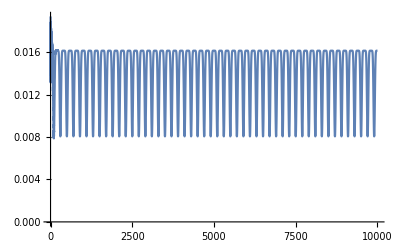

```mathematica
ListLinePlot[TRBDF2αList[[1]], PlotRange->All]
```

```mathematica
TRBDF2Pos = {};
For[i = 1, i ≤  numSteps + 1, 
posInfo = Sum[TRBDF2αList[[j]][[i]]*evecs[[j]],{j, 1, n}];
posInfo = (Transpose[projM].posInfo);
AppendTo[TRBDF2Pos, posInfo];
i++];
```

```mathematica
theoPos[(100 - 1) * h]
```

{0.,0.0649814,0.125649,0.210302,0.317466}

```mathematica
(*Plot α*)
totalPlots = {};
IEPlots = {};
NMPlots = {};
BDF2Plots = {};
TRBDF2Plots = {};
For[i = 1, i≤ n, 
λ = evals[[i]]//N;
theotimeα = Table[{m h, (theoαList[[i]]/. {t-> m h})}, {m, 0, numSteps}];
IEtimeα = Table[{timeList[[m]], IEαList[[i]][[m]]}, {m, 1, numSteps + 1}];
NMtimeα = Table[{timeList[[m]], NMαList[[i]][[m]]}, {m, 1, numSteps + 1}];
BDF2timeα = Table[{timeList[[m]], BDF2αList[[i]][[m]]}, {m, 1, numSteps + 1}];
TRBDF2timeα = Table[{timeList[[m]], TRBDF2αList[[i]][[m]]}, {m, 1, numSteps + 1}];
Print[λ];
totalPlot = ListLinePlot[{theotimeα, IEtimeα, BDF2timeα, NMtimeα, TRBDF2timeα}, PlotRange->All, PlotLegends->{"Theoretic", "IE", "BDF2", "NM","TRBDF2"}, ImageSize->Large];
IEPlot = ListLinePlot[{theotimeα, IEtimeα}, PlotRange->All, PlotLegends->{"Theoretic", "IE"}, ImageSize->Large];
BDF2Plot = ListLinePlot[{theotimeα, BDF2timeα}, PlotRange->All, PlotLegends->{"Theoretic", "BDF2"}, ImageSize->Large];
NMPlot = ListLinePlot[{theotimeα, NMtimeα}, PlotRange->All, PlotLegends->{"Theoretic", "NM"}, ImageSize->Large];
TRBDF2Plot = ListLinePlot[{theotimeα, TRBDF2timeα}, PlotRange->All, PlotLegends->{"Theoretic","TRBDF2"}, ImageSize->Large];
AppendTo[totalPlots, totalPlot];
AppendTo[IEPlots, IEPlot];
AppendTo[BDF2Plots, BDF2Plot];
AppendTo[NMPlots, NMPlot];
AppendTo[TRBDF2Plots, TRBDF2Plot];

dirname =  FileNameJoin[{NotebookDirectory[],"plots_Y_" <> ToString[youngs//N]  <> "/h_" <>ToString[h//N]<>"/numSegs_" <>ToString[n]<>"/lambda_" <> ToString[λ//N]}];
Switch[FileType[dirname],None,CreateDirectory[dirname] (*create dir*),Directory,Null (*do nothing*),File,Print["File with same name already exists!!"] (*error!*)];
filePrefex = dirname<> "/external_force_h_" <> ToString[h//N] <>"_lambda_" <> ToString[λ//N] <> "_sin_pow_" <> ToString[pow];
Export[filePrefex<>"_total_plots.png", totalPlot, ImageSize->1200,"CompressionLevel"->0];
Export[filePrefex<>"_IE_plots.png", IEPlot,ImageSize->1200,"CompressionLevel"->0];
Export[filePrefex<>"_BDF2_plots.png",BDF2Plot, ImageSize->1200,"CompressionLevel"->0];
Export[filePrefex<>"_NM_plots.png",NMPlot, ImageSize->1200,"CompressionLevel"->0];
Export[filePrefex<>"_TRBDF2_plots.png", TRBDF2Plot,ImageSize->1200,"CompressionLevel"->0];

ymax = TakeLargest[NMαList[[i]][[numSteps / 4;;numSteps / 4 + 1 / h]],1][[1]];
ymin = TakeSmallest[NMαList[[i]][[numSteps / 4;;numSteps / 4 + 1 / h]],1][[1]];
totalPlotZoomIn = ListLinePlot[{theotimeα, IEtimeα, BDF2timeα, NMtimeα, TRBDF2timeα}, PlotRange->{{totalTime / 4, totalTime / 4 + 1}, {ymin/1.2, ymax * 1.2}}, PlotLegends->{"Theoretic", "IE", "BDF2", "NM","TRBDF2"}, ImageSize->Large];
IEPlotZoomIn = ListLinePlot[{theotimeα, IEtimeα}, PlotRange->{{totalTime / 4, totalTime / 4 + 1},{ymin/1.2, ymax * 1.2}}, PlotLegends->{"Theoretic", "IE"}, ImageSize->Large];
BDF2PlotZoomIn = ListLinePlot[{theotimeα, BDF2timeα}, PlotRange->{{totalTime / 4, totalTime / 4 + 1},{ymin/1.2, ymax * 1.2}}, PlotLegends->{"Theoretic", "BDF2"}, ImageSize->Large];
NMPlotZoomIn = ListLinePlot[{theotimeα, NMtimeα}, PlotRange->{{totalTime / 4, totalTime / 4 + 1},{ymin/1.2, ymax * 1.2}}, PlotLegends->{"Theoretic", "NM"}, ImageSize->Large];
TRBDF2PlotZoomIn = ListLinePlot[{theotimeα, TRBDF2timeα}, PlotRange->{{totalTime / 4, totalTime / 4 + 1},{ymin/1.2, ymax * 1.2}}, PlotLegends->{"Theoretic","TRBDF2"}, ImageSize->Large];

Export[filePrefex<>"_total_plots_zoomIn.png", totalPlotZoomIn, ImageSize->1200,"CompressionLevel"->0];
Export[filePrefex<>"_IE_plots_zoomIn.png", IEPlotZoomIn,ImageSize->1200,"CompressionLevel"->0];
Export[filePrefex<>"_BDF2_plots_zoomIn.png",BDF2PlotZoomIn, ImageSize->1200,"CompressionLevel"->0];
Export[filePrefex<>"_NM_plots_zoomIn.png",NMPlotZoomIn, ImageSize->1200,"CompressionLevel"->0];
Export[filePrefex<>"_TRBDF2_plots_zoomIn.png", TRBDF2PlotZoomIn,ImageSize->1200,"CompressionLevel"->0];
i++;
]
```

141284.

93891.9

40000.

4824.59

```mathematica
IEαListT = Transpose[IEαList];
BDF2αListT = Transpose[BDF2αList];
NMαListT = Transpose[NMαList];
TRBDF2αListT = Transpose[TRBDF2αList];

ListLinePlot[{BDF2αListT[[i]]}, PlotRange->{{totalTime / 4, totalTime / 4 + 1},{-1.2,1.2}}, ImageSize->Large]
```

-Graphics-

```mathematica
Length[BDF2αListT]
```

10001

```mathematica
Length[BDF2αList]
```

4

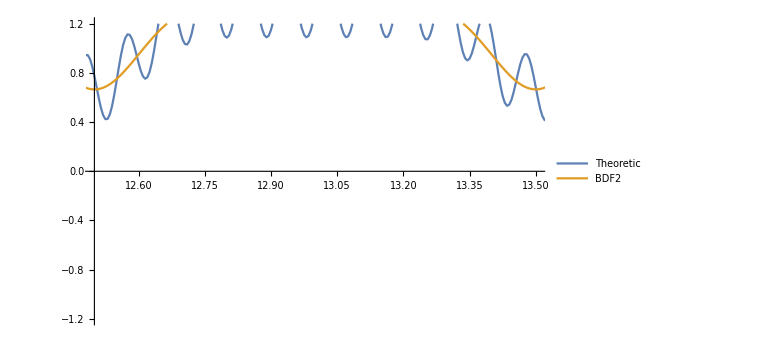

```mathematica
BDF2PlotZoomIn = ListLinePlot[{theotimeα, BDF2timeα}, PlotRange->{{totalTime / 4, totalTime / 4 + 1},{-1.2,1.2}}, PlotLegends->{"Theoretic", "BDF2"}, ImageSize->Large]
```

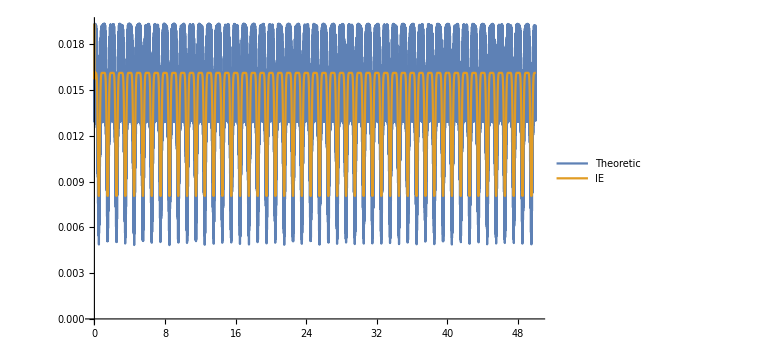

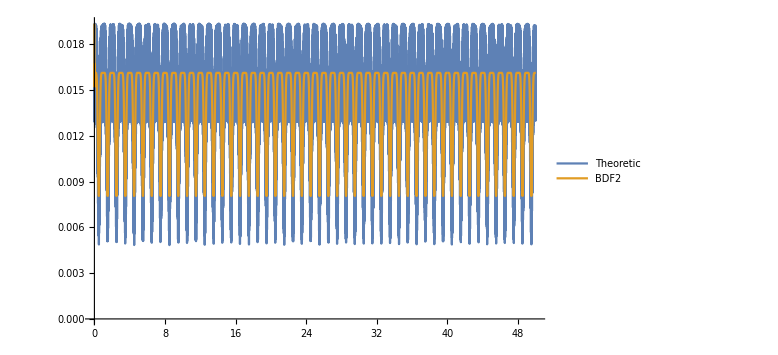

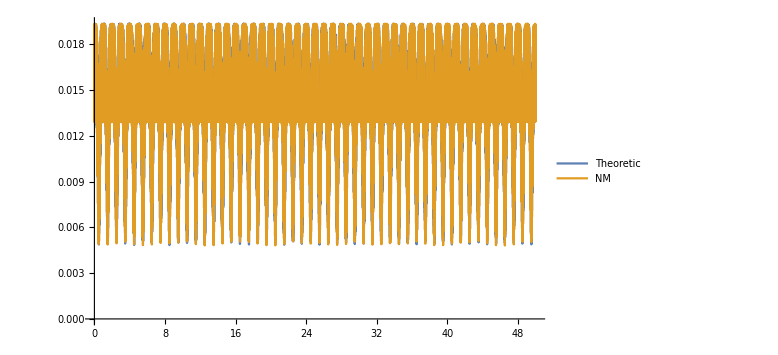

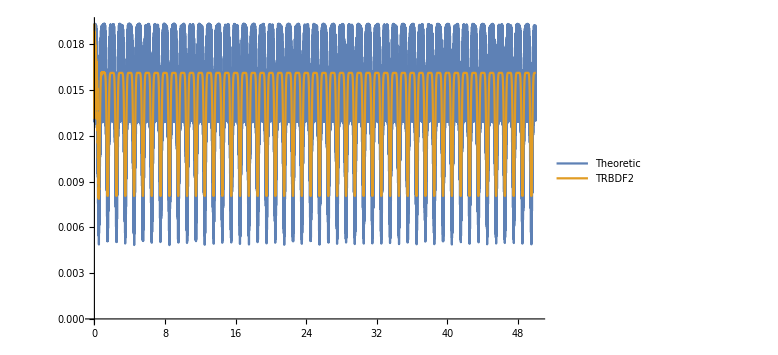

```mathematica
IEPlots[[1]]
BDF2Plots[[1]]
NMPlots[[1]]
TRBDF2Plots[[1]]
```

```mathematica
frameTheo =  Table[Point[Table[{theoPos[(m - 1) * h][[i]], 0}, {i, 1, n+1}]], {m , 1, numSteps + 1}];
```

```mathematica
frameIE = Table[Point[Table[{IEPos[[m]][[i]], -0.1}, {i, 1, n+1}]], {m, 1, numSteps + 1}];
frameNM = Table[Point[Table[{NMPos[[m]][[i]], -0.2}, {i, 1, n+1}]], {m, 1, numSteps + 1}];
frameBDF2 = Table[Point[Table[{BDF2Pos[[m]][[i]], -0.3}, {i, 1, n+1}]], {m, 1, numSteps + 1}];
frameTRBDF2 = Table[Point[Table[{TRBDF2Pos[[m]][[i]], -0.4}, {i, 1, n+1}]], {m, 1, numSteps + 1}];
```

```mathematica
Length[TRBDF2αList[[1]]]
```

10001

```mathematica
Animate[Graphics[{frameTheo[[m]], frameIE[[m]],frameBDF2[[m]],frameNM[[m]],frameTRBDF2[[m]]},  PlotRange->{{-.5,1.5}, {-0.5, 0.1}}, PlotRangeClipping->False],{m,1,numSteps + 1, 1}]
```